```mathematica
ineqs=Table[allGraphs[k,"comp"][allGraphs[k,"colofournull"],0],{k,Keys[allGraphs]}];Length[ineqs]
```

3

```mathematica
countDone=0;MyLeafCount[exp_]:=Block[{},countDone++;StringLength[ToString[exp]]]
```

```mathematica
ineqsW=Monitor[Simplify[Fold[And,ineqs],Trig->False,ComplexityFunction->MyLeafCount,Assumptions->nullAtomFacts],countDone];Length[ineqsW]
```

0

```mathematica
Length[ineqsW]
```

0

```mathematica
vars=ListofVars[Select[ineqsW,Length[ListofVars[#]]==2&]]
```

Select::normal: Nonatomic expression expected at position 1 in Select[True,Length[ListofVars[#1]]==2&].

{Select[True,Length[ListofVars[#1]]==2&]}

```mathematica
ineqs2=Table[allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0],{k,Keys[allGraphs]}];Length[ineqs]
```

3

```mathematica
ineqs2
```

{n1x2>0,-n12+n1x2>0,n12>0}

```mathematica
repcolofourrealnullgraph2
```

{n1x2→-Graphics-n1x20,n12→-Graphics-n122}

```mathematica
Table[allGraphs[k,"colofourrealnull"],{k,Keys[allGraphs]}]
```

{n1x2,-n12+n1x2,n12}

```mathematica
realnullAtomFacts=Table[allGraphs[k]["comp"][allGraphs[k]["colofourrealnull"],0],{k,realyNullAtomKeys}];Length[realnullAtomFacts]
```

2

```mathematica
ineqsW2=Monitor[Simplify[Fold[And,ineqs2],Trig->False,ComplexityFunction->MyLeafCount,Assumptions->realnullAtomFacts],countDone];Length[ineqsW2]
```

2

```mathematica
vars2=ListofVars[Select[ineqsW2,Length[ListofVars[#]]==2&]]
```

{True}

```mathematica
Graph[Map[#[[1]]->#[[2]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->"Name",GraphLayout->"BalloonEmbedding"]
```

-Graphics-

```mathematica
Graph[Map[#[[1]]->#[[2]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->Select[Table[allGraphs[k,"colofourrealnull"]->allGraphs[k,"graph"],{k,realyNullAtomKeys}],MemberQ[vars2,#[[1]]]&]]
```

-Graphics-

Select::normal: Nonatomic expression expected at position 1 in Select[True,Length[ListofVars[#1]]==2&].

Part::partd: Part specification True⟦1⟧ is longer than depth of object.

Part::partd: Part specification True⟦2⟧ is longer than depth of object.

Part::partw: Part 2 of Length[ListofVars[#1]]==2& does not exist.

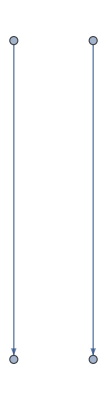

```mathematica
Graph[Map[#[[1]]->#[[2]]&,AndToTable[Select[ineqsW,Length[ListofVars[#]]==2&]]],VertexLabels->Select[Table[allGraphs[k,"colofournull"]->allGraphs[k,"graph"],{k,nullAtomKeys}],MemberQ[vars,#[[1]]]&]]
```

```mathematica
Take[ineqsW,5]
```

Take::normal: Nonatomic expression expected at position 1 in Take[True,5].

Take[True,5]

```mathematica
pairs=Subsets[nullAtomSymbols,{2}];Length[pairs]
```

1

```mathematica
Take[nullAtomFacts,3]
```

Take::take: Cannot take positions 1 through 3 in {v1x2>0,v12>0}.

Take[{v1x2>0,v12>0},3]

```mathematica
atomFactsAnd=Fold[And,nullAtomFacts]
```

v1x2>0&&v12>0

```mathematica
Monitor[Table[{p[[1]]>p[[2]]}->Length[ Simplify[p[[1]]>p[[2]]&&ineqsW,Trig->False,ComplexityFunction->MyLeafCount,Assumptions->nullAtomFacts]],{p,pairs}],Position[pairs, p]]
```

{{v1x2>v12}→2}

```mathematica
Select[nullAtomSymbols,!MemberQ[ListofVars[ Table[allGraphs[k,"colofournull"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]//Total//Expand],#]&]
```

{v1x2,v12}

```mathematica
Select[Keys[allGraphs],allGraphs[#,"colofournull"]==p1x2x3x4x5&]
```

{}

```mathematica
allGraphs[0,"graph"]
```

-Graphics-

```mathematica
allGraphs[quad1Key,"colofournull"]/.repcolofournullgraph2//Expand//Length
```

2

```mathematica
Select[nullAtomSymbols,!MemberQ[ListofVars[ Table[allGraphs[k,"colofournull"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]//Total//Expand],#]&]
```

{v1x2,v12}

```mathematica
Select[Keys[allGraphs],MemberQ[{p1x2x3x4x5,p1x25x34,p15x24x3,p14x23x5,p13x2x45,p12x35x4},allGraphs[#,"colofournull"]]&]
```

{}

```mathematica
allGraphs[6562,"graph"]
```

Missing[KeyAbsent,6562]